```mathematica
ass={r>0,z'[r]^2>0,CC>0}
```

{r>0,z'[r]^2>0,CC>0}

```mathematica
(*canoincal base vectors*)
```

```mathematica
ϵ[1]={1,0};
ϵ[2]={0,1};
```

```mathematica
g[r_]:={{1+(z'[r])^2,0},{0,r^2}}
```

```mathematica
detg[r_]:=Det[g[r]]
```

```mathematica
sqrtdetg[r_]:=Sqrt[detg[r]]
```

```mathematica
ig[r_]:=Inverse[g[r]]//FullSimplify
```

```mathematica
ig[r]
```

{{1/(1+z'[r]^2),0},{0,1/r^2}}

```mathematica
e[1][x_]:={Cos[x[[2]]], Sin[x[[2]]],z'[x[[1]]]} 
e[2][x_]:= {-x[[1]]Sin[x[[2]]],x[[1]] Cos[x[[2]]],0}
```

```mathematica
normal[x_]:=FullSimplify[Cross[e[1][x],e[2][x]]/sqrtdetg[x[[1]]],Assumptions->ass]
```

```mathematica
N3d[x_]:={-Cos[x[[2]]],-Sin[x[[2]]],0}
```

```mathematica
Clear[normNt]
```

```mathematica
Nt[r_]:=FullSimplify[Table[Sum[ig[r][[i,j]](N3d[{r,θ}].e[j][{r,θ}]),{j,1,2}],{i,1,2}],Assumptions->ass]
```

```mathematica
(*norm of Nt with respect to g*)
```

```mathematica
normNt[r_]:= Sqrt[Sum[Nt[r][[i]] Nt[r][[j]]*g[r][[i,j]],{i,1,2},{j,1,2}]]
```

```mathematica
Nt[r]/normNt[r]
```

{-√(1/(1+z'[r]^2)),0}

```mathematica
(*n^i at \partial \Omega_r*)
```

```mathematica
nRmin[x_]:=FullSimplify[{-x[[1]]/sqrtdetg[x[[1]]],0},Assumptions->ass]
```

```mathematica
(*n^i at \partial \Omega_R*)
```

```mathematica
nRmax[x_]:=FullSimplify[{x[[1]]/sqrtdetg[x[[1]]],0},Assumptions->ass]
```

```mathematica
solzpRmin=Solve[nRmin[{Rmin,θ}].{z'[Rmin],0}==zpRmin,z'[Rmin]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{z'[Rmin]→-zpRmin/(√(1-zpRmin^2))},{z'[Rmin]→zpRmin/(√(1-zpRmin^2))}}

```mathematica
solzpRmax=Solve[nRmin[{Rmax,θ}].{z'[Rmax],0}==zpRmax,z'[Rmax]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{z'[Rmax]→-zpRmax/(√(1-zpRmax^2))},{z'[Rmax]→zpRmax/(√(1-zpRmax^2))}}

```mathematica
normal[{r,θ}]
```

{-(Cos[θ] z'[r])/(√(1+z'[r]^2)),-(Sin[θ] z'[r])/(√(1+z'[r]^2)),1/(√(1+z'[r]^2))}

```mathematica
(*second fundamental form b*)
```

```mathematica
Derivative[ϵ[1]][e[1]][{r,θ}].normal[{r,θ}]//FullSimplify
```

z''[r]/(√(1+z'[r]^2))

```mathematica
Derivative[ϵ[1]][e[2]][{r,θ}].normal[{r,θ}]//FullSimplify
```

0

```mathematica
Derivative[ϵ[2]][e[1]][{r,θ}].normal[{r,θ}]//FullSimplify
```

0

```mathematica
Derivative[ϵ[2]][e[2]][{r,θ}].normal[{r,θ}]//FullSimplify
```

(r z'[r])/(√(1+z'[r]^2))

```mathematica
b[r_]:={{Derivative[ϵ[1]][e[1]][{r,θ}].normal[{r,θ}],Derivative[ϵ[1]][e[2]][{r,θ}].normal[{r,θ}]},{Derivative[ϵ[2]][e[1]][{r,θ}].normal[{r,θ}],Derivative[ϵ[2]][e[2]][{r,θ}].normal[{r,θ}]}}//FullSimplify
```

```mathematica
H[r_]:=1/2 Tr[ig[r].b[r]]//FullSimplify
```

```mathematica
K[r_]:=Det[b[r]]/detg[r]//FullSimplify
```

```mathematica
(*this is the function which appears under derivative in - \Nabla_{LB} H*)
```

```mathematica
ϕ[r_]:=(r^2 H'[r])/sqrtdetg[r]
```

```mathematica
FullSimplify[ϕ'[r],Assumptions->ass]
```

```mathematica
eq=FullSimplify[{κ(-2 1/sqrtdetg[r] ϕ'[r]-4H[r](H[r]^2-K[r]))+2σ [r]H[r]==0},Assumptions->ass]
```

```mathematica
(*
z[r_]:=CC * r
FullSimplify[κ(-2 1/sqrtdetg[r] ϕ'[r]-4H[r](H[r]^2-K[r]))+2σ [r]H[r],Assumptions->ass]
FullSimplify[Solve[(CC (-((2+CC^2) κ)+2 (1+CC^2) r^2 σ[r]))/(2 (1+CC^2)^(3/2) r^3)==0,σ[r]][[1]],Assumptions->ass]
*)
```

```mathematica
(*z[r_]:=CC * r*)
```

```mathematica
κ=1;
CC=1/10;
σ[r_]:=((2+CC^2) κ)/(2 (1+CC^2) r^2)
Rmin=1;
Rmax=2;
zRmin=CC Rmin;
zRmax=CC Rmax;
zpRmin=CC;
zpRmax=CC;
```

```mathematica
bcs={z[Rmin]==zRmin,z[Rmax]==zRmax,z'[Rmin]==zpRmin,z'[Rmax]==zpRmax};
```

```mathematica
s=NDSolve[Flatten[{eq,bcs}],z,{r,Rmin,Rmax}]
```

{{z→InterpolatingFunction[…]}}

```mathematica
Clear[r]
```

```mathematica
err=Table[{r,(κ(-2 1/sqrtdetg[r] ϕ'[r]-4H[r](H[r]^2-K[r]))+2σ[r]H[r])/.s[[1]]},{r,Rmin,Rmax,0.01}]
```

```mathematica
Max[Table[Abs[err[[i,2]]],{i,1,Length[err]}]]
```

1.67623×10^-10

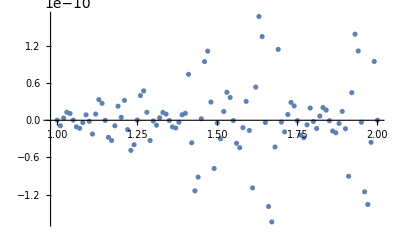

```mathematica
ListPlot[Table[{r,(κ(-2 1/sqrtdetg[r] ϕ'[r]-4H[r](H[r]^2-K[r]))+2σ[r]H[r])/.s[[1]]},{r,Rmin,Rmax,0.01}],PlotRange->Full]
```

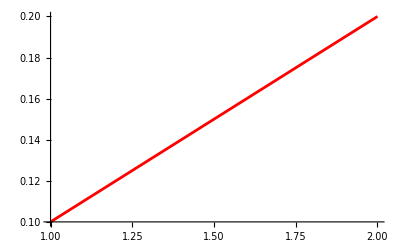

```mathematica
plotzex=Plot[Evaluate[z[r]/. s],{r,Rmin,Rmax},PlotRange->All, PlotStyle->Red]
```

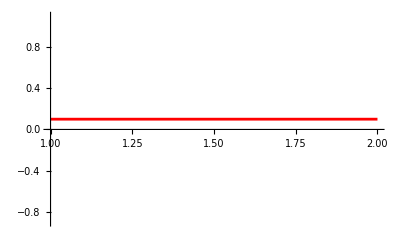

```mathematica
plotωex=Plot[Evaluate[z'[r]/. s],{r,Rmin,Rmax},PlotRange->All,PlotStyle->Red]
```

```mathematica
(*check z*)
```

```mathematica
znum=Import["~/Documents/finite_elements/solution/z.csv"];
znum=Table[{Sqrt[znum[[i,2]]^2+znum[[i,3]]^2],znum[[i,1]]},{i,2,Length[znum]}]
```

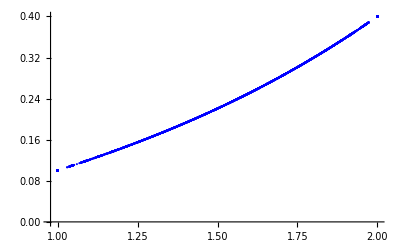

```mathematica
plotnum=ListPlot[znum,PlotRange->Full,PlotStyle->Blue]
```

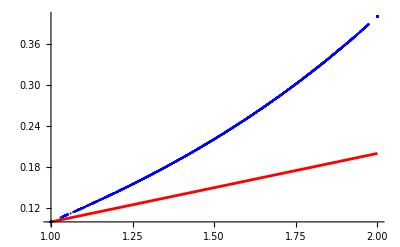

```mathematica
Show[plotzex,plotnum]
```

```mathematica
(*check ω*)
```

```mathematica
ω=Import["~/Documents/finite_elements/solution/omega.csv"];
ω=Table[{Sqrt[ω[[i,4]]^2+ω[[i,5]]^2],ω[[i,4]]/Sqrt[ω[[i,4]]^2+ω[[i,5]]^2] ω[[i,1]]+ω[[i,5]]/Sqrt[ω[[i,4]]^2+ω[[i,5]]^2] ω[[i,2]]},{i,2,Length[ω]}]
```

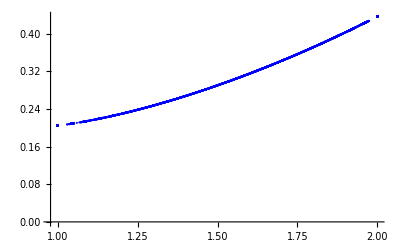

```mathematica
plotωnum=ListPlot[ω,PlotStyle->Blue]
```

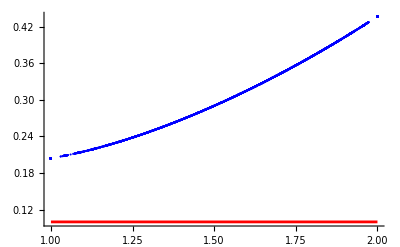

```mathematica
Show[plotωex,plotωnum]
```